```mathematica
GaussianPulse[t_,t0_,dt_,f_] := Piecewise[{{Exp[-(t-f-t0)^2/f^2*5],t<=f+t0},{1,t≥t0+f && t≤t0+f+dt },{Exp[-(t-t0-dt-f)^2/f^2*5],t>=t0+dt}}]
```

```mathematica
h={{-Δ/2,g},{g,Δ/2}}
```

{{-Δ/2,g},{g,Δ/2}}

```mathematica
Eigenvalues[h]
```

{-1/2 √(4 g^2+Δ^2),1/2 √(4 g^2+Δ^2)}

```mathematica
eq1= D[ϕ1[t],t]==-I*(-delta[t]/2*ϕ1[t]+g*ϕ2[t]);
eq2 = D[ϕ2[t],t] ==-I*(g*ϕ1[t]+delta[t]/2*ϕ2[t]);
```

```mathematica
resultf[dt_] := NDSolve[{eq1,eq2,ϕ1[0]==1,ϕ2[0]==0} //. {delta[t]->(1-GaussianPulse[t,0,20.,dt])*g*30,g->0.1*π},{ϕ1[t],ϕ2[t]},{t,0,100}]
```

```mathematica
result2[dt_]:= Abs[resultf[dt][[1]][[2]][[2]]]^2
```

```mathematica
FindMaximum[result2[0.4],{t,5}][[1]]
```

0.99594

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

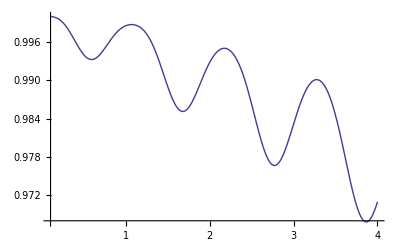

```mathematica
Plot[FindMaximum[result2[dt],{t,6}][[1]],{dt,0.1,4}]
```

```mathematica
result2[0.5]
```

Abs[InterpolatingFunction[{{0.,100.}},<>][t]]^2

```mathematica
amplitudes=Map[{#,result2[#][[1]] /.{t->5}} &,Range[0.1,4,0.05]]
```

{{0.1,0.999982},{0.15,0.999911},{0.2,0.99973},{0.25,0.999367},{0.3,0.998752},{0.35,0.997821},{0.4,0.996533},{0.45,0.994866},{0.5,0.992836},{0.55,0.99049},{0.6,0.987908},{0.65,0.985192},{0.7,0.982464},{0.75,0.979847},{0.8,0.977453},{0.85,0.975371},{0.9,0.973652},{0.95,0.972298},{1.,0.971263},{1.05,0.970445},{1.1,0.969698},{1.15,0.96884},{1.2,0.967669},{1.25,0.965979},{1.3,0.963581},{1.35,0.960317},{1.4,0.956083},{1.45,0.950834},{1.5,0.944597},{1.55,0.937469},{1.6,0.929622},{1.65,0.921286},{1.7,0.912736},{1.75,0.904274},{1.8,0.896201},{1.85,0.888789},{1.9,0.882256},{1.95,0.876741},{2.,0.872285},{2.05,0.868825},{2.1,0.866191},{2.15,0.864126},{2.2,0.862301},{2.25,0.860343},{2.3,0.85787},{2.35,0.85452},{2.4,0.849979},{2.45,0.844005},{2.5,0.836453},{2.55,0.827281},{2.6,0.816561},{2.65,0.804476},{2.7,0.791314},{2.75,0.777451},{2.8,0.763329},{2.85,0.749422},{2.9,0.7362},{2.95,0.72409},{3.,0.71343},{3.05,0.704431},{3.1,0.697158},{3.15,0.691512},{3.2,0.68724},{3.25,0.683959},{3.3,0.681194},{3.35,0.678419},{3.4,0.675104},{3.45,0.67076},{3.5,0.664968},{3.55,0.657411},{3.6,0.647891},{3.65,0.636343},{3.7,0.622834},{3.75,0.607566},{3.8,0.590864},{3.85,0.573164},{3.9,0.554987},{3.95,0.536913},{4.,0.519536}}

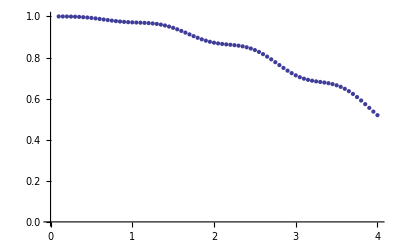

```mathematica
ListPlot[amplitudes]
```

```mathematica
maxima=Map[{#,FindMaximum[result2[#],{t,6}][[1]]}&,Range[0.1,4,0.05]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{{0.1,0.999965},{0.15,0.999835},{0.2,0.999525},{0.25,0.998967},{0.3,0.998143},{0.35,0.997097},{0.4,0.99594},{0.45,0.994828},{0.5,0.993926},{0.55,0.993371},{0.6,0.99324},{0.65,0.993533},{0.7,0.994175},{0.75,0.99504},{0.8,0.995984},{0.85,0.996875},{0.9,0.997621},{0.95,0.998173},{1.,0.998525},{1.05,0.998682},{1.1,0.998651},{1.15,0.998414},{1.2,0.997934},{1.25,0.997155},{1.3,0.996035},{1.35,0.994566},{1.4,0.9928},{1.45,0.990858},{1.5,0.988921},{1.55,0.987205},{1.6,0.985916},{1.65,0.985213},{1.7,0.985169},{1.75,0.985762},{1.8,0.986874},{1.85,0.988328},{1.9,0.989923},{1.95,0.991468},{2.,0.992816},{2.05,0.993873},{2.1,0.994589},{2.15,0.994943},{2.2,0.994927},{2.25,0.994523},{2.3,0.993704},{2.35,0.992443},{2.4,0.990734},{2.45,0.988616},{2.5,0.98619},{2.55,0.983628},{2.6,0.981159},{2.65,0.979039},{2.7,0.977503},{2.75,0.976726},{2.8,0.97678},{2.85,0.977626},{2.9,0.979119},{2.95,0.981044},{3.,0.983154},{3.05,0.985218},{3.1,0.987047},{3.15,0.988504},{3.2,0.98951},{3.25,0.99002},{3.3,0.990012},{3.35,0.989464},{3.4,0.988361},{3.45,0.986694},{3.5,0.98449},{3.55,0.981826},{3.6,0.978846},{3.65,0.97577},{3.7,0.972863},{3.75,0.970418},{3.8,0.968697},{3.85,0.967882},{3.9,0.968046},{3.95,0.969132},{4.,0.970972}}

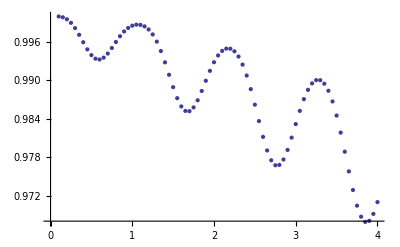

```mathematica
ListPlot[maxima]
```

```mathematica
maximafit=Fit[Map[{#[[1]],#[[2]]-1}&,maxima],{t,t^2},t]
```

-0.00342332 t-0.000769996 t^2

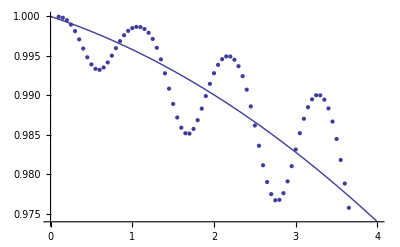

```mathematica
Show[Plot[maximafit+1,{t,0,4},PlotRange->Full],ListPlot[maxima,PlotRange->Full]]
```

```mathematica
maximaandfit=Map[{#[[1]],#[[2]],maximafit+1 /. {t->#[[1]]}}&,maxima];
```

```mathematica
Export[NotebookDirectory[]<>"swap_error_gaussian_pulse.csv", maximaandfit]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_error_gaussian_pulse.csv

```mathematica
result2[0.1] /.{t->0.1}
```

0.000955387

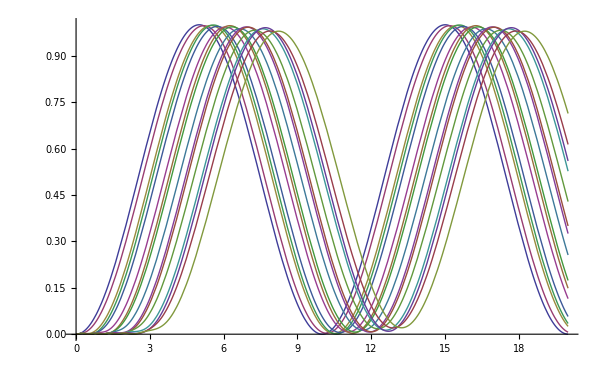

```mathematica
Plot[Evaluate[{Map[result2[#]&,Range[0.1,4,0.25]]}],{t,0,20},PlotRange->Full]
```

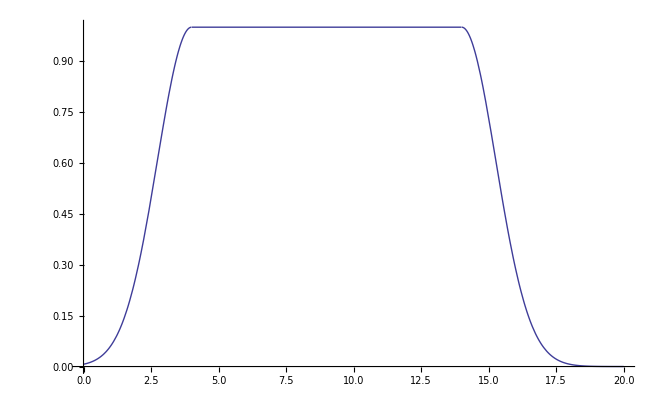

```mathematica
Plot[GaussianPulse[t,0,10,4],{t,0,20}]
```